# Triangular Automata

## Mathematica Package

This notebook aims to show the functionalities of the Triangular Automata package. This second version of the package is much more efficient but lacks some v1 features. I will add them back gradually.
More information: https://triangular-automata.net

Paul Cousin
https://orcid.org/0000-0002-3866-7615

## Setup

First, run the following command to import the package.

```mathematica
<<"https://code.triangular-automata.net/TriangularAutomata.wl";
```

## Grid

In this package, grids have the header TAGrid. There are a few predefined grids that you can use.

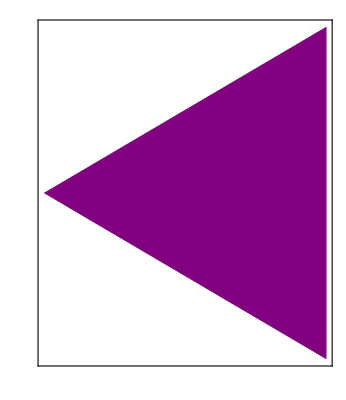
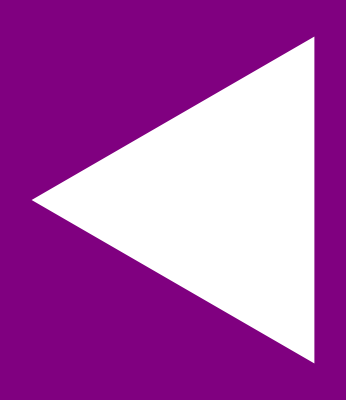
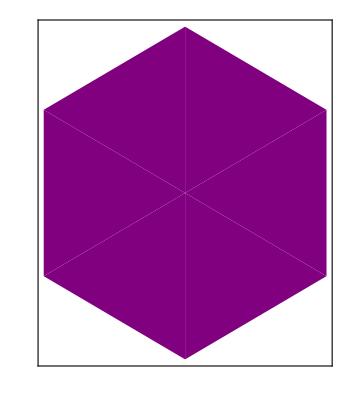
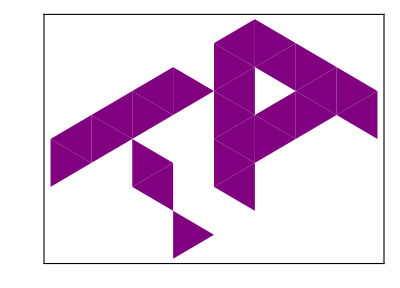

```mathematica
{TAGrid[1],TAGrid[0],TAGrid["Hexagon"],TAGrid["TA"]}
```

TANegative[grid] returns the negative grid.

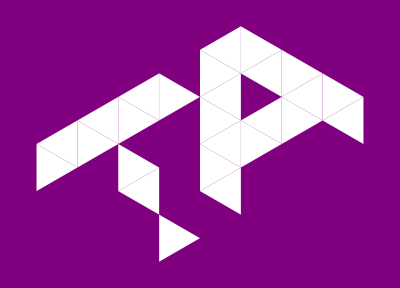

```mathematica
TANegative@TAGrid["TA"]
```

You can also define your own grid by using a matrix.

```mathematica
TAGrid[{{1,1},{1,1},{1,1}}]
```

-Graphics-

The second argument of TAGrid is the state of the universe.

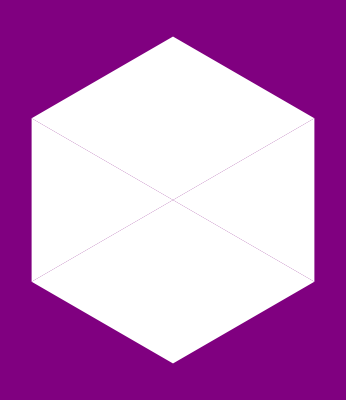

```mathematica
TAGrid[{{0,0},{0,0},{0,0}},1,0]
```

The third is the phase of the top-left triangle: 0 if it points to the left, 1 if it points to the right.

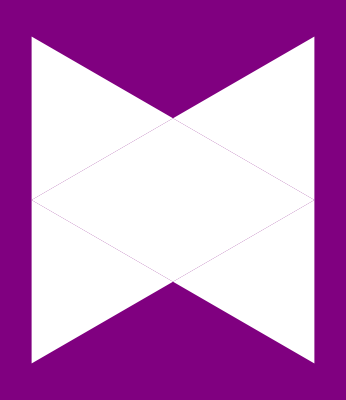

```mathematica
TAGrid[{{0,0},{0,0},{0,0}},1,1]
```

You can generate random x-by-y grids with TARandom[{x,y}].

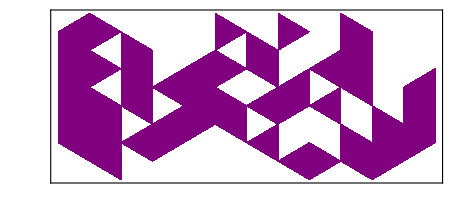

```mathematica
TARandom[{12,8}]
```

The optional parameters are, the density, the state of the universe and the phase of the grid.

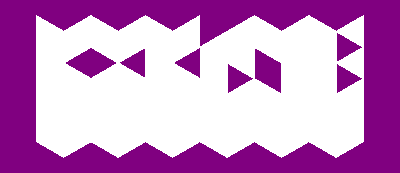

```mathematica
TARandom[{12,8},.9,1,1]
```

The function TAEdit[grid] opens a pop-up window to edit the grid.

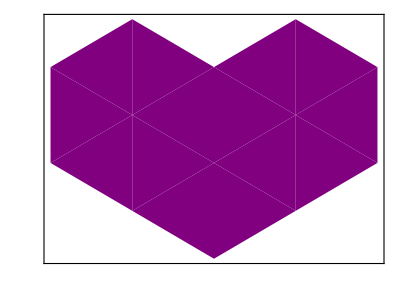

```mathematica
TAEdit@TARandom[{6,6},0]
```

## Evolution

The function TAEvolve serves to apply a rule to a grid.

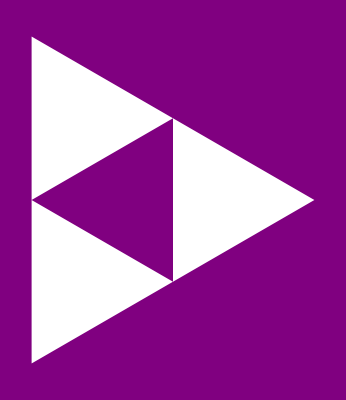

```mathematica
TAEvolve[TAGrid[1],181]
```

The third argument indicates the number of times the rule should be applied.

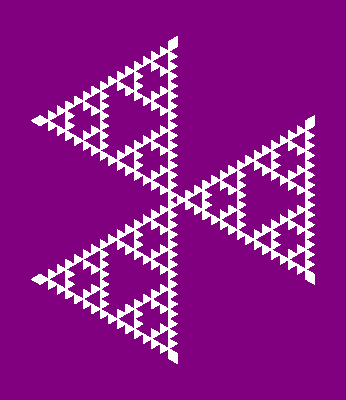

```mathematica
TAEvolve[TAGrid[1],181,32]
```

If you place it in curly brackets, the function returns the list of grids.

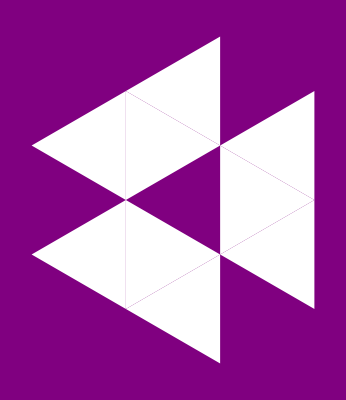
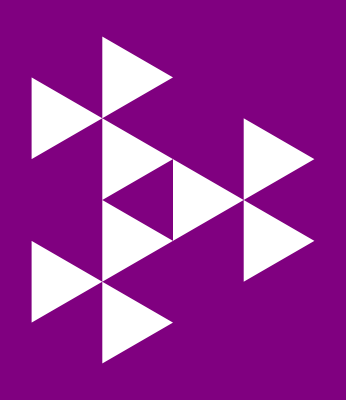
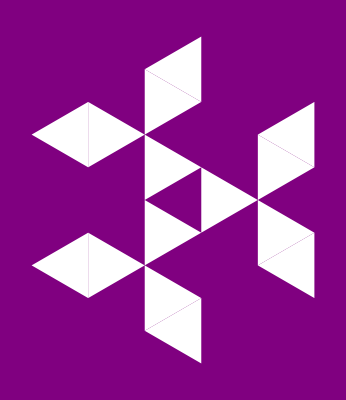
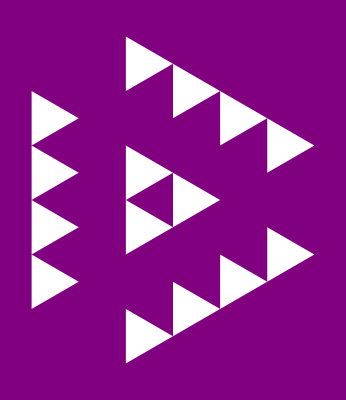
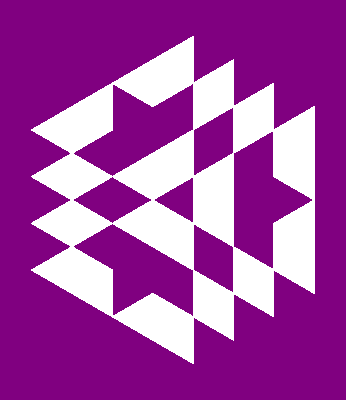
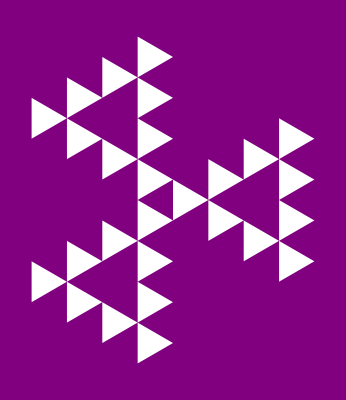
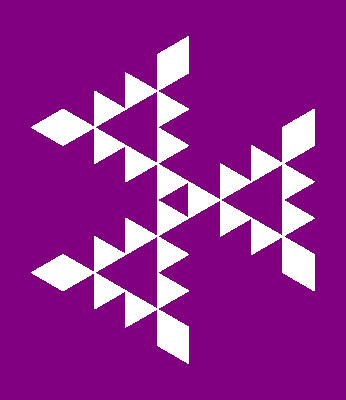
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TAEvolve[TAGrid[1], 181,{8}]
```

If you give a list of rule numbers, the rules will alternate.

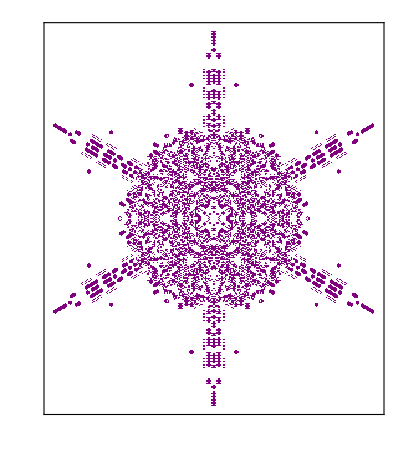

```mathematica
TAEvolve[-Graphics-,{88,150},512]
```

## Plots

To plot a grid, use the function TAPlot.

```mathematica
TAPlot@-Graphics-
```

-Graphics-

If the grid is very large, you can use TAQuickPlot to render the grid much more efficiently at the expense of details.

```mathematica
TAQuickPlot@TAEvolve[TAGrid["Hexagon"],53,2048]
```

-Graphics-

You can also make plot for rules using TARulePlot[rule].

```mathematica
TARulePlot[210]
```

-Graphics-

## Utilities

TAPopulation[grid] will return the number of cells in the grid that have the opposite state to the universe.

```mathematica
TAPopulation@-Graphics-
```

17568

TADestroboscopify[rule] will return the rules to alternate to obtain a similar behavior as the rule be without the stroboscopic effect.

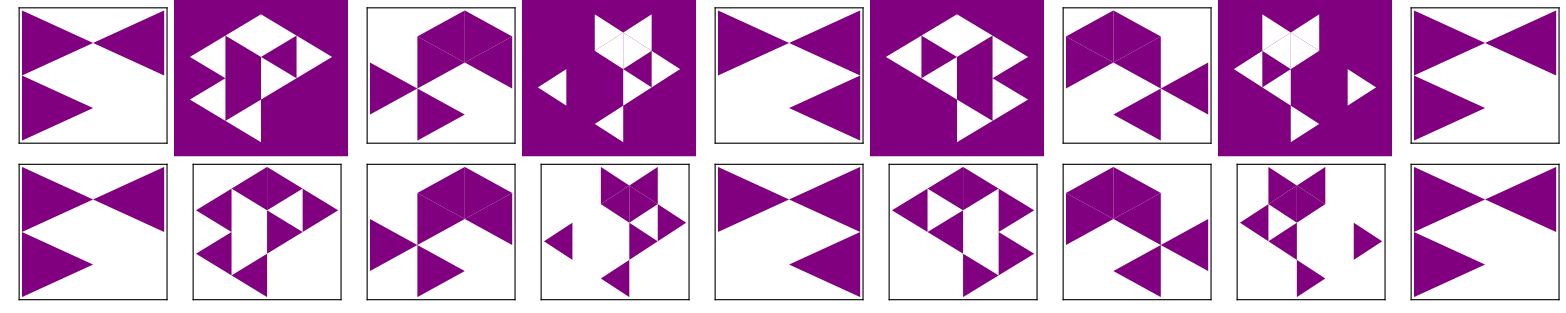

```mathematica
Grid[TAEvolve[TAGrid[{{1,1},{0,0},{1,0}},0,1],#,{8}]&/@{53,TADestroboscopify[53]}]
```